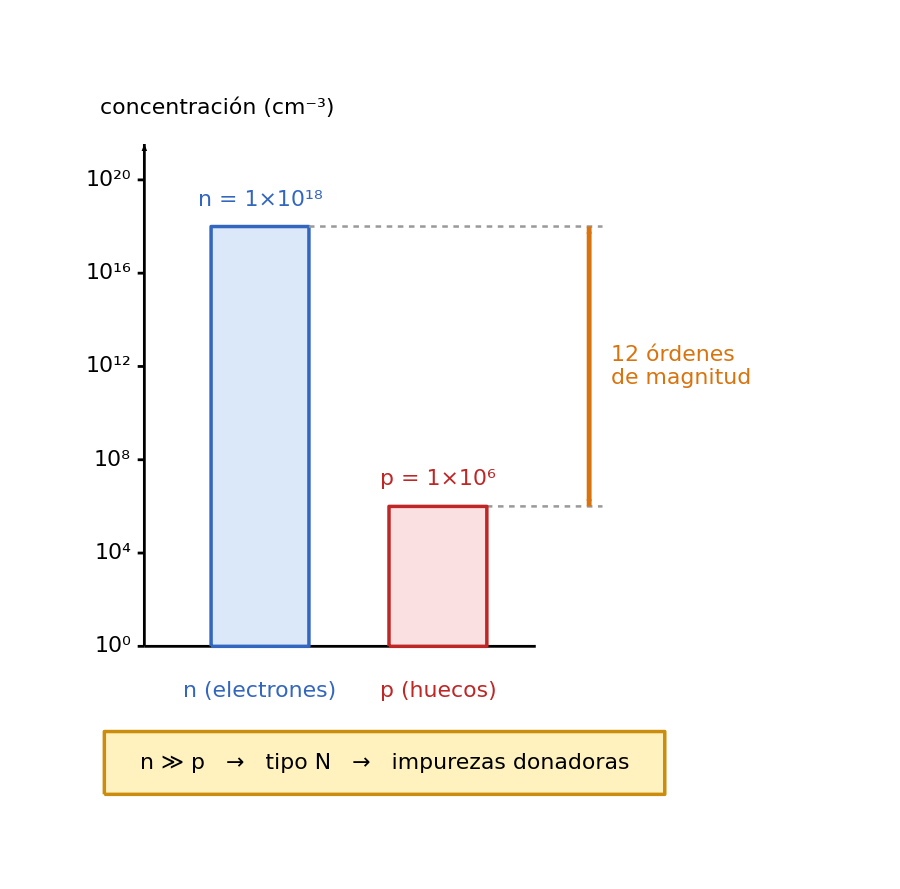

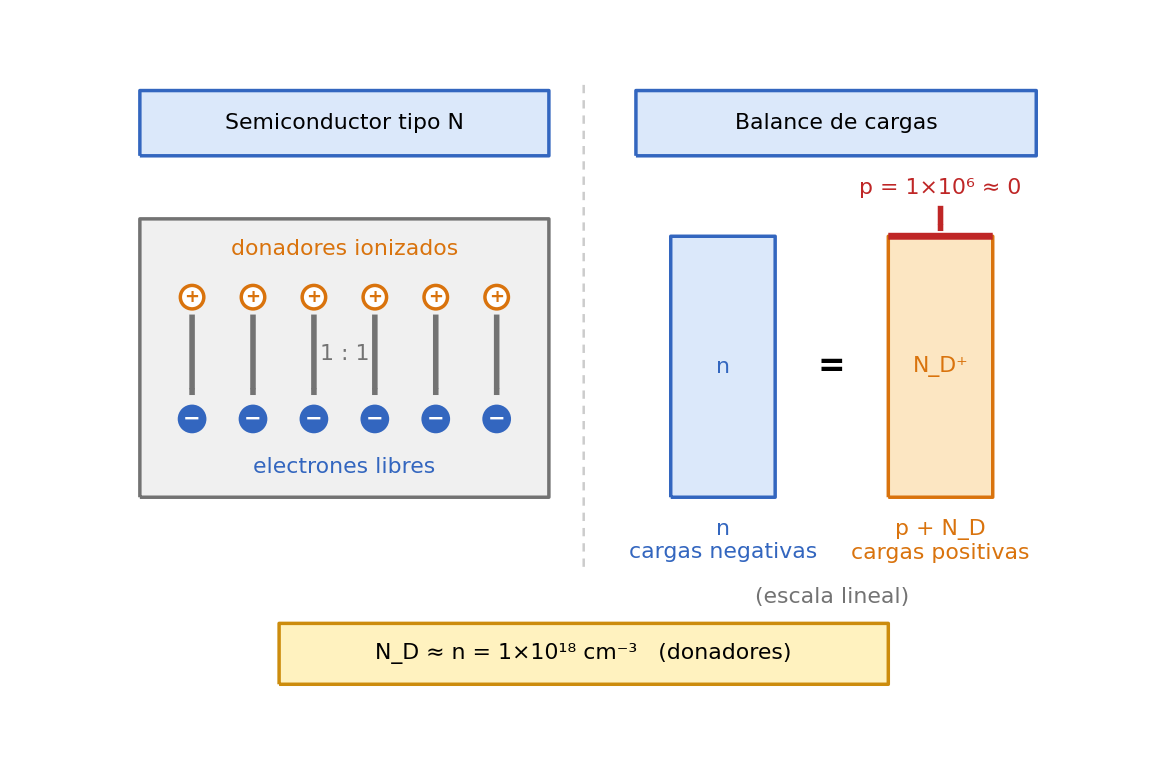

```mathematica
{diagramaTipoDopado,diagramaNeutralidadN}=Module[{fs,mostrarValores,cAzul,cAzulB,cRojo,cRojoF,cNar,cNarF,cGris,cOro,cOroB,nn,pp,ND,ord,ins,insI,insD,flecha,caja,carga,ionR,cient,y0,sy,YL,xa,xn,xp,hw,xar,g1,yb0,Hb,xb1,xb2,hwb,hND,hp,g2},(*----------Parámetros globales----------*)fs=22;(*tamaño de fuente único para todo el gráfico*)mostrarValores=True;(*False oculta los valores numéricos*)cAzul=RGBColor[0.86,0.91,0.98];cAzulB=RGBColor[0.20,0.40,0.75];
cRojo=RGBColor[0.75,0.15,0.15];cRojoF=RGBColor[0.98,0.88,0.88];
cNar=RGBColor[0.85,0.45,0.05];cNarF=RGBColor[0.99,0.90,0.76];
cGris=GrayLevel[0.45];
cOro=RGBColor[1.0,0.95,0.75];cOroB=RGBColor[0.80,0.55,0.05];
(*----------Datos del problema (cm^-3)----------*)nn=1.*10.^18;pp=1.*10.^6;
ND=nn-pp;(*neutralidad con ionización total:n=p+N_D*)ord=Round[Log10[nn/pp]];(*órdenes de magnitud entre n y p*)(*----------Funciones auxiliares----------*)ins[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos];
insI[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Left,Center}];
insD[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Right,Center}];
flecha[p1_,p2_,col_,s_:0.022]:={col,AbsoluteThickness[4],Arrowheads[s],Arrow[{p1,p2}]};
caja[{xc_,yc_},{w_,h_},relleno_,borde_]:={EdgeForm[{AbsoluteThickness[2.5],borde}],relleno,Rectangle[{xc-w/2,yc-h/2},{xc+w/2,yc+h/2},RoundingRadius->0.15]};
carga[pos_,signo_,col_]:={col,Disk[pos,0.33],Text[Style[signo,Round[0.95 fs],Bold,White],pos]};
ionR[pos_,signo_,col_]:={White,Disk[pos,0.27],col,AbsoluteThickness[2.5],Circle[pos,0.27],Text[Style[signo,Round[0.8 fs],Bold,col],pos]};
cient[x_]:=Module[{ex=Floor[Log10[x]+10.^-9],m},m=Round[x/10.^ex,0.01];
Row[{If[m==Round[m],Round[m],NumberForm[m,{3,2},NumberPoint->","]],"×",Superscript["10",ex]}]];
(* =====Figura 1:tipo de semiconductor (n frente a p,escala logarítmica)=====*)y0=2.0;sy=0.52;
YL[l_]:=y0+sy l;(*l=log10 de la concentración*)xa=1.6;xn=4.2;xp=8.2;hw=1.1;xar=11.6;
g1=Graphics[{(*eje logarítmico*){Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{xa,y0},{xa,13.2}}]},{Black,AbsoluteThickness[2],Line[{{xa,y0},{xp+2.2,y0}}]},insI[Row[{"concentración (",Superscript["cm","−3"],")"}],{0.6,14.0}],Table[{Black,AbsoluteThickness[2],Line[{{xa-0.15,YL[k]},{xa,YL[k]}}],insD[Row[{Superscript["10",k]}],{xa-0.3,YL[k]}]},{k,0,20,4}],(*barras de n y de p*){EdgeForm[{AbsoluteThickness[2.5],cAzulB}],cAzul,Rectangle[{xn-hw,y0},{xn+hw,YL[Log10[nn]]}]},{EdgeForm[{AbsoluteThickness[2.5],cRojo}],cRojoF,Rectangle[{xp-hw,y0},{xp+hw,YL[Log10[pp]]}]},ins[Row[{Style["n",Italic],If[mostrarValores,Row[{" = ",cient[nn]}],""]}],{xn,YL[Log10[nn]]+0.6},cAzulB],ins[Row[{Style["p",Italic],If[mostrarValores,Row[{" = ",cient[pp]}],""]}],{xp,YL[Log10[pp]]+0.6},cRojo],ins[Row[{Style["n",Italic]," (electrones)"}],{xn,1.0},cAzulB],ins[Row[{Style["p",Italic]," (huecos)"}],{xp,1.0},cRojo],(*distancia entre ambas concentraciones*){GrayLevel[0.6],AbsoluteThickness[1.8],AbsoluteDashing[{4,4}],Line[{{xn+hw,YL[Log10[nn]]},{xar+0.3,YL[Log10[nn]]}}],Line[{{xp+hw,YL[Log10[pp]]},{xar+0.3,YL[Log10[pp]]}}]},{cNar,AbsoluteThickness[3.5],Arrowheads[{-0.016,0.016}],Arrow[{{xar,YL[Log10[pp]]},{xar,YL[Log10[nn]]}}]},insI[Column[{If[mostrarValores,Row[{ord," órdenes"}],"órdenes"],"de magnitud"},Left],{xar+0.5,(YL[Log10[pp]]+YL[Log10[nn]])/2},cNar],(*conclusión*)caja[{7.0,-0.6},{12.6,1.4},cOro,cOroB],ins[Row[{Style["n",Italic]," ≫ ",Style["p",Italic],"   →   tipo N   →   impurezas donadoras"}],{7.0,-0.6}]},ImageSize->900,PlotRange->{{0.2,16.6},{-1.6,14.6}},PlotRangePadding->None,AspectRatio->16.2/16.4,Background->White];
(* =====Figura 2:neutralidad de carga n=p+N_D (ionización total)=====*)yb0=3.6;Hb=6.0;xb1=14.4;xb2=19.4;hwb=1.2;
hND=Hb ND/nn;hp=Hb pp/nn;(*alturas en escala lineal*)g2=Graphics[{(*cabeceras y separador*)caja[{5.7,12.2},{9.4,1.5},cAzul,cAzulB],ins["Semiconductor tipo N",{5.7,12.2}],caja[{17.0,12.2},{9.2,1.5},cAzul,cAzulB],ins["Balance de cargas",{17.0,12.2}],{GrayLevel[0.8],AbsoluteThickness[1.8],AbsoluteDashing[{6,5}],Line[{{11.2,2.0},{11.2,13.2}}]},(*cristal:cada donador ionizado cede un electrón libre*){GrayLevel[0.94],EdgeForm[{AbsoluteThickness[2.5],cGris}],Rectangle[{1.0,3.6},{10.4,10.0}]},ins["donadores ionizados",{5.7,9.3},cNar],ins["electrones libres",{5.7,4.3},cAzulB],Table[{ionR[{2.2+1.4 k,8.2},"+",cNar],flecha[{2.2+1.4 k,7.8},{2.2+1.4 k,5.95},cGris,0.012],carga[{2.2+1.4 k,5.4},"−",cAzulB]},{k,0,5}],ins["1 : 1",{5.7,6.9},cGris],(*barras:n frente a p+N_D (escala lineal)*){EdgeForm[{AbsoluteThickness[2.5],cAzulB}],cAzul,Rectangle[{xb1-hwb,yb0},{xb1+hwb,yb0+Hb}]},{EdgeForm[{AbsoluteThickness[2.5],cNar}],cNarF,Rectangle[{xb2-hwb,yb0},{xb2+hwb,yb0+hND}]},{cRojo,AbsoluteThickness[5],Line[{{xb2-hwb,yb0+hND+hp},{xb2+hwb,yb0+hND+hp}}]},ins[Style["n",Italic],{xb1,yb0+Hb/2},cAzulB],ins[Row[{Subsuperscript["N","D","+"]}],{xb2,yb0+hND/2},cNar],Text[Style["=",Round[1.5 fs],Bold],{(xb1+xb2)/2,yb0+Hb/2}],(*el hueco es invisible a esta escala*)flecha[{xb2,yb0+Hb+0.7},{xb2,yb0+hND+0.12},cRojo,0.014],ins[Row[{Style["p",Italic],If[mostrarValores,Row[{" = ",cient[pp]}],""]," ≈ 0"}],{xb2,yb0+Hb+1.1},cRojo],(*etiquetas bajo las barras*)ins[Column[{Style["n",Italic],"cargas negativas"},Center],{xb1,2.6},cAzulB],ins[Column[{Row[{Style["p",Italic]," + ",Subscript["N","D"]}],"cargas positivas"},Center],{xb2,2.6},cNar],ins["(escala lineal)",{(xb1+xb2)/2,1.3},cGris],(*resultado*)caja[{11.2,0.0},{14.0,1.4},cOro,cOroB],ins[Row[{Subscript["N","D"]," ≈ ",Style["n",Italic],If[mostrarValores,Row[{" = ",cient[ND]," ",Superscript["cm","−3"]}],""],"   (donadores)"}],{11.2,0.0}]},ImageSize->1150,PlotRange->{{0.2,21.8},{-1.2,13.4}},PlotRangePadding->None,AspectRatio->14.6/21.6,Background->White];
{g1,g2}];
diagramaTipoDopado
diagramaNeutralidadN
```

```mathematica
Export["T2_P2_a.png",diagramaTipoDopado,Background->None,ImageResolution->300,ImageSize->800];
Export["T2_P2_b.png",diagramaNeutralidadN,Background->None,ImageResolution->300,ImageSize->800];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T2_P2_a.png"]]]
```

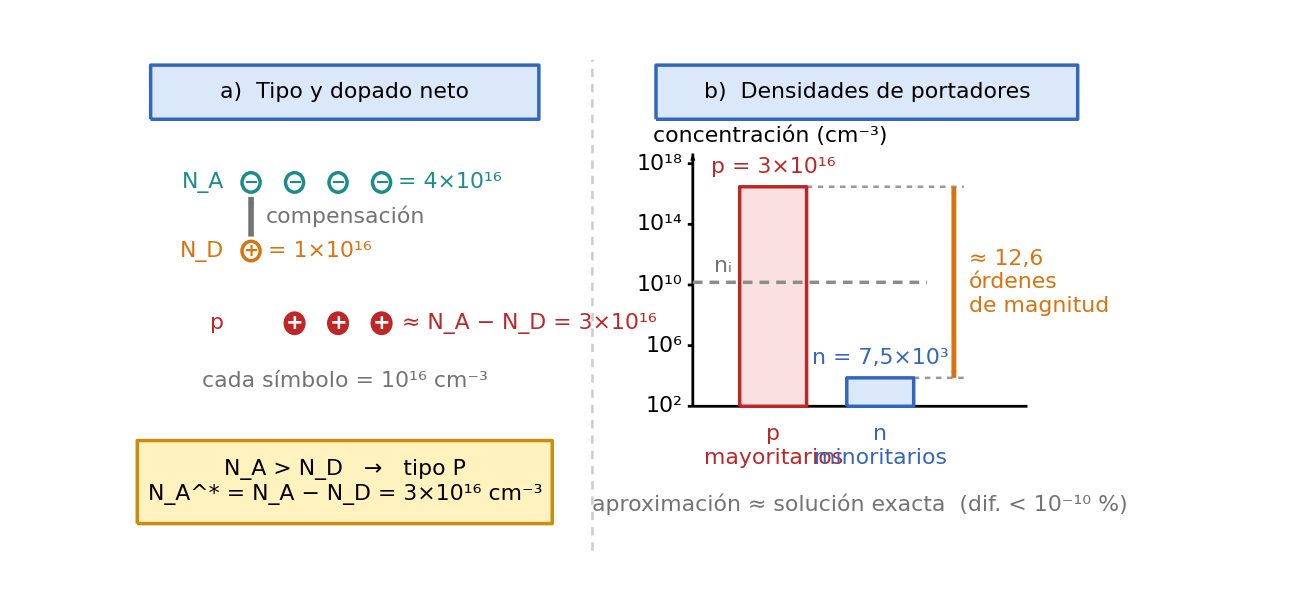

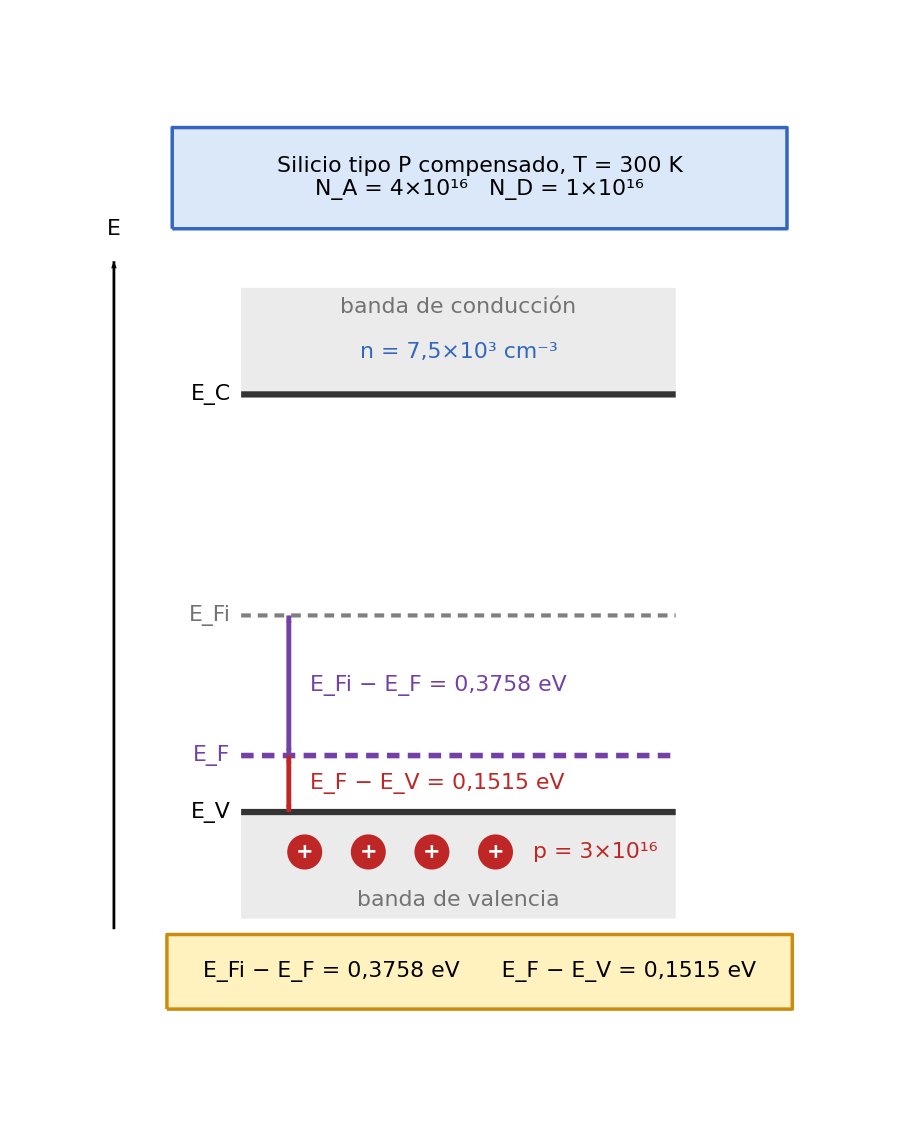

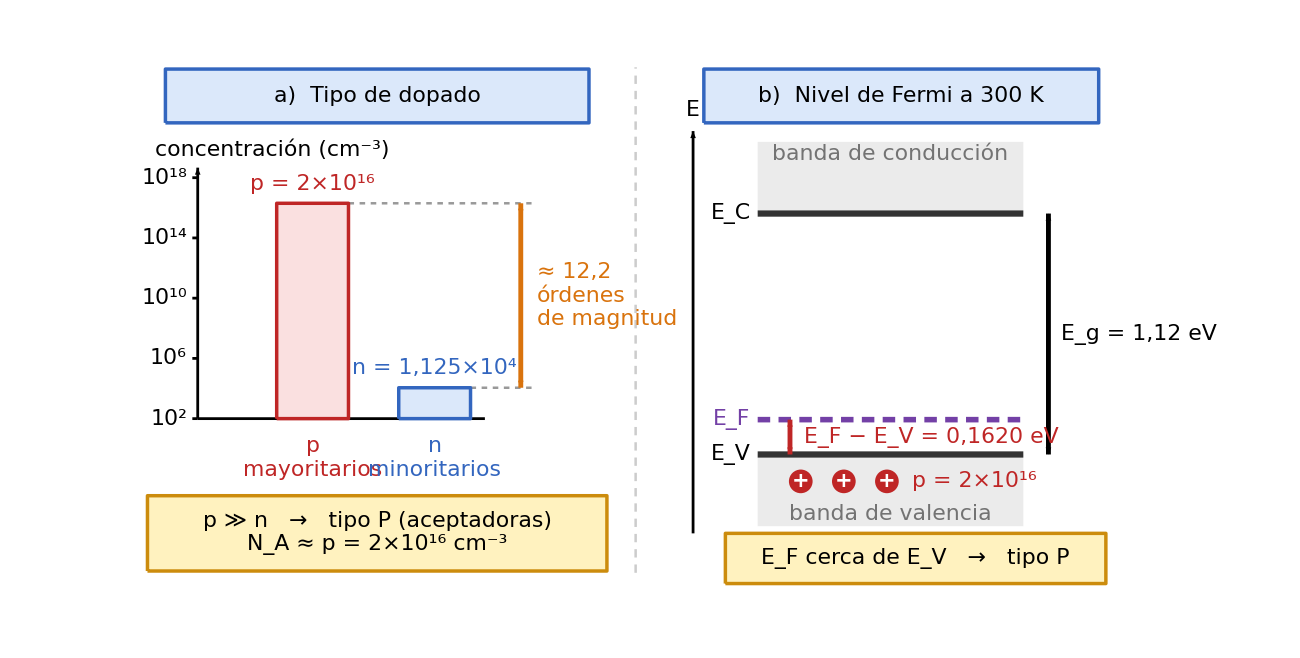

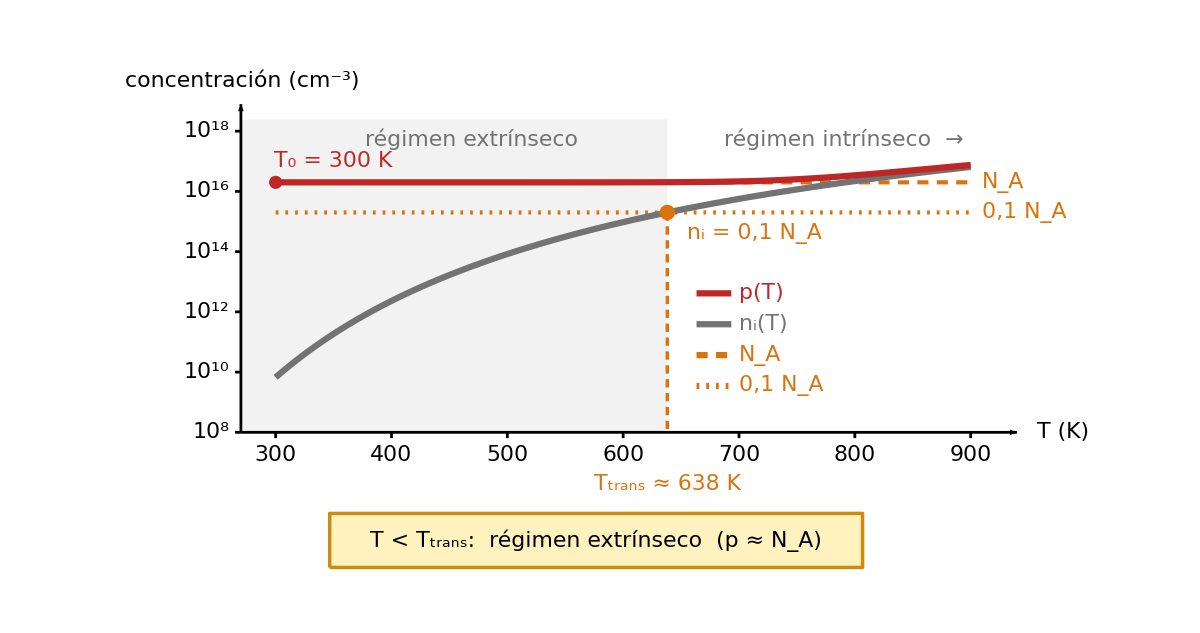

```mathematica
{diagramaP1ab,diagramaP1c,diagramaP2ab,diagramaP2c}=Module[{fs,mostrarValores,cAzul,cAzulB,cRojo,cRojoF,cVio,cNar,cTeal,cGris,cOro,cOroB,kT,ni0,Nv0,ins,insI,insD,flecha,caja,carga,ionR,cota,cient,dec,ord,hband,YL,y0b,syb,NAc,NDc,ud,nA,nD,nNet,pEx,nMin,xs0,dx,ox,xP,xN,xa,hw,g1,Egd,se,yV,yC,dFV,dFiF,dFiV,yF,yFi,px,wb,g2,pp,nn,NAp,Eg2,dFV2,se2,yV2,yC2,yF2,px2,wb2,g3,NcT,NvT,EgS,kB,niT,pT,tk,Tt,XT,YT,y0t,syt,curvaNi,curvaP,markX,markY,items,g4},(*----------Parámetros globales----------*)fs=22;(*tamaño de fuente único para todo el gráfico*)mostrarValores=True;(*False oculta los valores numéricos calculados*)cAzul=RGBColor[0.86,0.91,0.98];cAzulB=RGBColor[0.20,0.40,0.75];
cRojo=RGBColor[0.75,0.15,0.15];cRojoF=RGBColor[0.98,0.88,0.88];
cVio=RGBColor[0.45,0.25,0.65];cNar=RGBColor[0.85,0.45,0.05];
cTeal=RGBColor[0.10,0.55,0.55];cGris=GrayLevel[0.45];
cOro=RGBColor[1.0,0.95,0.75];cOroB=RGBColor[0.80,0.55,0.05];
(*----------Funciones auxiliares----------*)ins[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos];
insI[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Left,Center}];
insD[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Right,Center}];
flecha[p1_,p2_,col_,s_:0.02]:={col,AbsoluteThickness[4],Arrowheads[s],Arrow[{p1,p2}]};
caja[{xc_,yc_},{w_,h_},relleno_,borde_]:={EdgeForm[{AbsoluteThickness[2.5],borde}],relleno,Rectangle[{xc-w/2,yc-h/2},{xc+w/2,yc+h/2},RoundingRadius->0.15]};
carga[pos_,signo_,col_]:={col,Disk[pos,0.33],Text[Style[signo,Round[0.95 fs],Bold,White],pos]};
ionR[pos_,signo_,col_]:={White,Disk[pos,0.27],col,AbsoluteThickness[2.5],Circle[pos,0.27],Text[Style[signo,Round[0.8 fs],Bold,col],pos]};
cota[x_,y1_,y2_,col_]:={col,AbsoluteThickness[3.5],Arrowheads[{-0.014,0.014}],Arrow[{{x,y1},{x,y2}}]};
cient[x_]:=Module[{ex=Floor[Log10[x]+10.^-9],m},m=Round[x/10.^ex,0.001];
Row[{If[m==Round[m],Round[m],NumberForm[m,NumberPoint->","]],"×",Superscript["10",ex]}]];
dec[x_,k_]:=NumberForm[x,{5,k},NumberPoint->","];
ord[x_]:=NumberForm[Round[x,0.1],{3,1},NumberPoint->","];
hband[px_,wb_,yv_,yc_]:={{GrayLevel[0.92],EdgeForm[None],Rectangle[{px,yc},{px+wb,yc+2.}],Rectangle[{px,yv-2.},{px+wb,yv}]},{GrayLevel[0.2],AbsoluteThickness[4.5],Line[{{px,yc},{px+wb,yc}}],Line[{{px,yv},{px+wb,yv}}]},ins["banda de conducción",{px+wb/2,yc+1.65},cGris],ins["banda de valencia",{px+wb/2,yv-1.65},cGris],insD[Row[{Subscript["E","C"]}],{px-0.2,yc}],insD[Row[{Subscript["E","V"]}],{px-0.2,yv}]};
(*----------Datos comunes (eV,cm^-3)----------*)kT=0.0259;ni0=1.5*10.^10;Nv0=1.04*10.^19;
y0b=5.2;syb=0.42;(*gráfico logarítmico de barras*)YL[c_]:=y0b+syb (Log10[c]-2);
(* =====Problema 1,apartados a) y b)=====*)NAc=4.*10.^16;NDc=1.*10.^16;ud=10.^16;
nA=Round[NAc/ud];nD=Round[NDc/ud];nNet=nA-nD;
pEx=(NAc-NDc)/2+Sqrt[((NAc-NDc)/2)^2+ni0^2];(*solución cuadrática exacta*)nMin=ni0^2/pEx;
{xs0,dx}={4.2,1.3};
{ox,xP,xN,xa,hw}={17.4,19.8,23.0,25.2,1.0};
g1=Graphics[{{GrayLevel[0.8],AbsoluteThickness[1.8],AbsoluteDashing[{6,5}],Line[{{14.4,1.2},{14.4,14.8}}]},(*a) compensación de impurezas*)caja[{7.0,13.9},{11.6,1.5},cAzul,cAzulB],ins[Row[{Style["a",Bold],")  Tipo y dopado neto"}],{7.0,13.9}],insD[Row[{Subscript["N","A"]}],{3.4,11.4},cTeal],Table[ionR[{xs0+dx i,11.4},"−",cTeal],{i,0,nA-1}],insD[Row[{Subscript["N","D"]}],{3.4,9.5},cNar],Table[ionR[{xs0+dx i,9.5},"+",cNar],{i,0,nD-1}],Table[flecha[{xs0+dx i,9.9},{xs0+dx i,11.0},cGris,0.012],{i,0,nD-1}],insI["compensación",{xs0+0.45,10.45},cGris],insD[Style["p",Italic],{3.4,7.5},cRojo],Table[carga[{xs0+dx i,7.5},"+",cRojo],{i,nD,nA-1}],If[mostrarValores,{insI[Row[{" = ",cient[NAc]}],{xs0+dx (nA-1)+0.5,11.4},cTeal],insI[Row[{" = ",cient[NDc]}],{xs0+0.5,9.5},cNar]},{}],insI[Row[{" ≈ ",Subscript["N","A"]," − ",Subscript["N","D"],If[mostrarValores,Row[{" = ",cient[NAc-NDc]}],""]}],{xs0+dx (nA-1)+0.6,7.5},cRojo],ins[Row[{"cada símbolo = ",Superscript["10",Round[Log10[ud]]]," ",Superscript["cm","−3"]}],{7.0,5.9},cGris],caja[{7.0,3.1},{12.4,2.3},cOro,cOroB],ins[Column[{Row[{Subscript["N","A"]," > ",Subscript["N","D"],"   →   tipo P"}],Row[{Subsuperscript["N","A","*"]," = ",Subscript["N","A"]," − ",Subscript["N","D"],If[mostrarValores,Row[{" = ",cient[NAc-NDc]," ",Superscript["cm","−3"]}],""]}]},Center],{7.0,3.1}],(*b) densidades de portadores*)caja[{22.6,13.9},{12.6,1.5},cAzul,cAzulB],ins[Row[{Style["b",Bold],")  Densidades de portadores"}],{22.6,13.9}],{Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{ox,y0b},{ox,12.2}}]},{Black,AbsoluteThickness[2],Line[{{ox,y0b},{27.4,y0b}}]},insI[Row[{"concentración (",Superscript["cm","−3"],")"}],{ox-1.2,12.7}],Table[{Black,AbsoluteThickness[2],Line[{{ox-0.15,YL[10.^k]},{ox,YL[10.^k]}}],insD[Row[{Superscript["10",k]}],{ox-0.3,YL[10.^k]}]},{k,{2,6,10,14,18}}],{EdgeForm[{AbsoluteThickness[2.5],cRojo}],cRojoF,Rectangle[{xP-hw,y0b},{xP+hw,YL[pEx]}]},{EdgeForm[{AbsoluteThickness[2.5],cAzulB}],cAzul,Rectangle[{xN-hw,y0b},{xN+hw,YL[nMin]}]},{GrayLevel[0.55],AbsoluteThickness[2.5],AbsoluteDashing[{7,5}],Line[{{ox,YL[ni0]},{24.4,YL[ni0]}}]},ins[Row[{Subscript["n","i"]}],{ox+0.9,YL[ni0]+0.45},cGris],ins[Row[{Style["p",Italic],If[mostrarValores,Row[{" = ",cient[pEx]}],""]}],{xP,YL[pEx]+0.55},cRojo],ins[Row[{Style["n",Italic],If[mostrarValores,Row[{" = ",cient[nMin]}],""]}],{xN,YL[nMin]+0.55},cAzulB],ins[Column[{Style["p",Italic],"mayoritarios"},Center],{xP,4.1},cRojo],ins[Column[{Style["n",Italic],"minoritarios"},Center],{xN,4.1},cAzulB],{GrayLevel[0.6],AbsoluteThickness[1.8],AbsoluteDashing[{4,4}],Line[{{xP+hw,YL[pEx]},{xa+0.3,YL[pEx]}}],Line[{{xN+hw,YL[nMin]},{xa+0.3,YL[nMin]}}]},{cNar,AbsoluteThickness[3.5],Arrowheads[{-0.014,0.014}],Arrow[{{xa,YL[nMin]},{xa,YL[pEx]}}]},insI[Column[{If[mostrarValores,Row[{"≈ ",ord[Log10[pEx/nMin]]}],""],"órdenes","de magnitud"},Left],{xa+0.45,(YL[nMin]+YL[pEx])/2},cNar],ins[Row[{"aproximación ≈ solución exacta  (dif. < ",Superscript["10","−10"]," %)"}],{22.4,2.5},cGris]},ImageSize->1300,PlotRange->{{0.2,29.6},{1.0,14.9}},PlotRangePadding->None,AspectRatio->13.9/29.4,Background->White];
(* =====Problema 1,apartado c):posición del nivel de Fermi=====*)Egd=1.12;se=7.;yV=3.6;yC=yV+se Egd;(*E_g solo fija la escala del dibujo*)dFV=kT Log[Nv0/pEx];dFiF=kT Log[pEx/ni0];dFiV=dFV+dFiF;
yF=yV+se dFV;yFi=yV+se dFiV;
px=3.4;wb=8.2;
g2=Graphics[{caja[{px+wb/2+0.4,15.5},{11.6,1.9},cAzul,cAzulB],ins[Column[{"Silicio tipo P compensado, T = 300 K",If[mostrarValores,Row[{Subscript["N","A"]," = ",cient[NAc],"   ",Subscript["N","D"]," = ",cient[NDc]}],""]},Center],{px+wb/2+0.4,15.5}],{Black,AbsoluteThickness[2],Arrowheads[0.018],Arrow[{{1.0,yV-2.2},{1.0,yC+2.5}}]},ins[Style["E",Italic],{1.0,yC+3.1}],hband[px,wb,yV,yC],{GrayLevel[0.5],AbsoluteThickness[3],AbsoluteDashing[{7,5}],Line[{{px,yFi},{px+wb,yFi}}]},{cVio,AbsoluteThickness[4],AbsoluteDashing[{9,6}],Line[{{px,yF},{px+wb,yF}}]},insD[Row[{Subscript["E","Fi"]}],{px-0.2,yFi},cGris],insD[Row[{Subscript["E","F"]}],{px-0.2,yF},cVio],cota[px+0.9,yV,yF,cRojo],insI[Row[{Subscript["E","F"]," − ",Subscript["E","V"],If[mostrarValores,Row[{" = ",dec[dFV,4]," eV"}],""]}],{px+1.3,(yV+yF)/2},cRojo],cota[px+0.9,yF,yFi,cVio],insI[Row[{Subscript["E","Fi"]," − ",Subscript["E","F"],If[mostrarValores,Row[{" = ",dec[dFiF,4]," eV"}],""]}],{px+1.3,(yF+yFi)/2},cVio],Table[carga[{px+ddx,yV-0.75},"+",cRojo],{ddx,{1.2,2.4,3.6,4.8}}],insI[Row[{Style["p",Italic],If[mostrarValores,Row[{" = ",cient[pEx]}],""]}],{px+5.5,yV-0.75},cRojo],ins[Row[{Style["n",Italic],If[mostrarValores,Row[{" = ",cient[nMin]," ",Superscript["cm","−3"]}]," ≈ 0"]}],{px+wb/2,yC+0.8},cAzulB],caja[{px+wb/2+0.4,0.6},{11.8,1.4},cOro,cOroB],ins[If[mostrarValores,Row[{Subscript["E","Fi"]," − ",Subscript["E","F"]," = ",dec[dFiF,4]," eV      ",Subscript["E","F"]," − ",Subscript["E","V"]," = ",dec[dFV,4]," eV"}],Row[{Subscript["E","F"]," bajo ",Subscript["E","Fi"],", cerca de ",Subscript["E","V"]}]],{px+wb/2+0.4,0.6}]},ImageSize->900,PlotRange->{{0.4,14.2},{-0.5,16.9}},PlotRangePadding->None,AspectRatio->17.4/13.8,Background->White];
(* =====Problema 2,apartados a) y b)=====*)pp=2.*10.^16;nn=1.125*10.^4;NAp=pp-nn;
Eg2=1.12;dFV2=kT Log[Nv0/pp];
se2=6.;yV2=4.2;yC2=yV2+se2 Eg2;yF2=yV2+se2 dFV2;
px2=18.0;wb2=7.4;
{ox,xP,xN,xa,hw}={2.4,5.6,9.0,11.4,1.0};
g3=Graphics[{{GrayLevel[0.8],AbsoluteThickness[1.8],AbsoluteDashing[{6,5}],Line[{{14.6,0.9},{14.6,15.0}}]},(*a) tipo de dopado*)caja[{7.4,14.2},{11.8,1.5},cAzul,cAzulB],ins[Row[{Style["a",Bold],")  Tipo de dopado"}],{7.4,14.2}],{Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{ox,y0b},{ox,12.2}}]},{Black,AbsoluteThickness[2],Line[{{ox,y0b},{10.4,y0b}}]},insI[Row[{"concentración (",Superscript["cm","−3"],")"}],{ox-1.2,12.7}],Table[{Black,AbsoluteThickness[2],Line[{{ox-0.15,YL[10.^k]},{ox,YL[10.^k]}}],insD[Row[{Superscript["10",k]}],{ox-0.3,YL[10.^k]}]},{k,{2,6,10,14,18}}],{EdgeForm[{AbsoluteThickness[2.5],cRojo}],cRojoF,Rectangle[{xP-hw,y0b},{xP+hw,YL[pp]}]},{EdgeForm[{AbsoluteThickness[2.5],cAzulB}],cAzul,Rectangle[{xN-hw,y0b},{xN+hw,YL[nn]}]},ins[Row[{Style["p",Italic],If[mostrarValores,Row[{" = ",cient[pp]}],""]}],{xP,YL[pp]+0.55},cRojo],ins[Row[{Style["n",Italic],If[mostrarValores,Row[{" = ",cient[nn]}],""]}],{xN,YL[nn]+0.55},cAzulB],ins[Column[{Style["p",Italic],"mayoritarios"},Center],{xP,4.1},cRojo],ins[Column[{Style["n",Italic],"minoritarios"},Center],{xN,4.1},cAzulB],{GrayLevel[0.6],AbsoluteThickness[1.8],AbsoluteDashing[{4,4}],Line[{{xP+hw,YL[pp]},{xa+0.3,YL[pp]}}],Line[{{xN+hw,YL[nn]},{xa+0.3,YL[nn]}}]},{cNar,AbsoluteThickness[3.5],Arrowheads[{-0.014,0.014}],Arrow[{{xa,YL[nn]},{xa,YL[pp]}}]},insI[Column[{If[mostrarValores,Row[{"≈ ",ord[Log10[pp/nn]]}],""],"órdenes","de magnitud"},Left],{xa+0.45,(YL[nn]+YL[pp])/2},cNar],caja[{7.4,2.0},{12.8,2.1},cOro,cOroB],ins[Column[{Row[{Style["p",Italic]," ≫ ",Style["n",Italic],"   →   tipo P (aceptadoras)"}],If[mostrarValores,Row[{Subscript["N","A"]," ≈ ",Style["p",Italic]," = ",cient[pp]," ",Superscript["cm","−3"]}],""]},Center],{7.4,2.0}],(*b) nivel de Fermi a 300 K*)caja[{22.0,14.2},{11.0,1.5},cAzul,cAzulB],ins[Row[{Style["b",Bold],")  Nivel de Fermi a 300 K"}],{22.0,14.2}],{Black,AbsoluteThickness[2],Arrowheads[0.018],Arrow[{{16.2,yV2-2.2},{16.2,yC2+2.3}}]},ins[Style["E",Italic],{16.2,yC2+2.9}],hband[px2,wb2,yV2,yC2],{cVio,AbsoluteThickness[4],AbsoluteDashing[{9,6}],Line[{{px2,yF2},{px2+wb2,yF2}}]},insD[Row[{Subscript["E","F"]}],{px2-0.2,yF2},cVio],cota[px2+0.9,yV2,yF2,cRojo],insI[Row[{Subscript["E","F"]," − ",Subscript["E","V"],If[mostrarValores,Row[{" = ",dec[dFV2,4]," eV"}],""]}],{px2+1.3,(yV2+yF2)/2},cRojo],cota[px2+wb2+0.7,yV2,yC2,Black],insI[Row[{Subscript["E","g"]," = ",dec[Eg2,2]," eV"}],{px2+wb2+1.05,(yV2+yC2)/2}],Table[carga[{px2+ddx,yV2-0.75},"+",cRojo],{ddx,{1.2,2.4,3.6}}],insI[Row[{Style["p",Italic],If[mostrarValores,Row[{" = ",cient[pp]}],""]}],{px2+4.3,yV2-0.75},cRojo],caja[{22.4,1.3},{10.6,1.4},cOro,cOroB],ins[Row[{Subscript["E","F"]," cerca de ",Subscript["E","V"],"   →   tipo P"}],{22.4,1.3}]},ImageSize->1300,PlotRange->{{0.2,29.8},{0.2,15.2}},PlotRangePadding->None,AspectRatio->15./29.6,Background->White];
(* =====Problema 2,apartado c):temperatura de transición=====*)NcT=2.8*10.^19;NvT=1.04*10.^19;EgS=1.12;kB=8.6173*10.^-5;
niT[t_]:=Sqrt[NcT NvT] (t/300.)^1.5 Exp[-EgS/(2 kB t)];
pT[t_]:=NAp/2+Sqrt[(NAp/2)^2+niT[t]^2];
Tt=tk/. FindRoot[Log[niT[tk]]-Log[0.1 NAp]==0,{tk,640.}];
{y0t,syt}={3.2,0.78};
XT[t_]:=3.2+0.03 (t-250.);
YT[c_]:=y0t+syt (Log10[c]-8);
curvaNi=Table[{XT[t],YT[niT[t]]},{t,300.,900.,5.}];
curvaP=Table[{XT[t],YT[pT[t]]},{t,300.,900.,5.}];
markX=XT[Tt];markY=YT[0.1 NAp];
items={{cRojo,{},Row[{Style["p",Italic],"(",Style["T",Italic],")"}]},{GrayLevel[0.45],{},Row[{Subscript["n","i"],"(",Style["T",Italic],")"}]},{cNar,{8,6},Row[{Subscript["N","A"]}]},{cNar,{2,5},Row[{"0,1 ",Subscript["N","A"]}]}};
g4=Graphics[{(*zona extrínseca (hasta T_trans)*){GrayLevel[0.95],EdgeForm[None],Rectangle[{XT[270.],y0t},{markX,11.3}]},ins["régimen extrínseco",{XT[(300.+Tt)/2],10.8},cGris],ins[Row[{"régimen intrínseco  →"}],{XT[790.],10.8},cGris],(*ejes*){Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{XT[270.],y0t},{XT[940.],y0t}}],Arrow[{{XT[270.],y0t},{XT[270.],11.7}}]},ins[Row[{Style["T",Italic]," (K)"}],{XT[940.]+1.2,y0t}],insI[Row[{"concentración (",Superscript["cm","−3"],")"}],{0.8,12.3}],Table[{Black,AbsoluteThickness[2],Line[{{XT[270.]-0.15,YT[10.^k]},{XT[270.],YT[10.^k]}}],insD[Row[{Superscript["10",k]}],{XT[270.]-0.3,YT[10.^k]}]},{k,8,18,2}],Table[{Black,AbsoluteThickness[2],Line[{{XT[t],y0t},{XT[t],y0t-0.15}}],ins[ToString[Round[t]],{XT[t],y0t-0.6}]},{t,300.,900.,100.}],(*N_A y 0,1 N_A*){cNar,AbsoluteThickness[3],AbsoluteDashing[{8,6}],Line[{{XT[300.],YT[NAp]},{XT[900.],YT[NAp]}}]},{cNar,AbsoluteThickness[3],AbsoluteDashing[{2,5}],Line[{{XT[300.],YT[0.1 NAp]},{XT[900.],YT[0.1 NAp]}}]},insI[Row[{Subscript["N","A"]}],{XT[900.]+0.3,YT[NAp]},cNar],insI[Row[{"0,1 ",Subscript["N","A"]}],{XT[900.]+0.3,YT[0.1 NAp]},cNar],(*curvas n_i(T) y p(T)*){GrayLevel[0.45],AbsoluteThickness[4.5],Line[curvaNi]},{cRojo,AbsoluteThickness[4.5],Line[curvaP]},{cRojo,Disk[{XT[300.],YT[pT[300.]]},0.17]},ins[Row[{Subscript["T","0"]," = 300 K"}],{XT[300.]+1.5,YT[NAp]+0.55},cRojo],(*temperatura de transición*){cNar,AbsoluteThickness[2.5],AbsoluteDashing[{6,4}],Line[{{markX,markY},{markX,y0t}}]},{cNar,Disk[{markX,markY},0.2]},insI[Row[{Subscript["n","i"]," = 0,1 ",Subscript["N","A"]}],{markX+0.5,markY-0.55},cNar],ins[Row[{Subscript["T","trans"],If[mostrarValores,Row[{" ≈ ",Round[Tt]," K"}],""]}],{markX,y0t-1.35},cNar],(*leyenda*)Table[{items[[k,1]],AbsoluteThickness[4.5],AbsoluteDashing[items[[k,2]]],Line[{{15.6,6.8-0.8 (k-1)},{16.5,6.8-0.8 (k-1)}}],insI[items[[k,3]],{16.7,6.8-0.8 (k-1)},items[[k,1]]]},{k,4}],(*conclusión*)caja[{13.0,0.4},{13.8,1.4},cOro,cOroB],ins[Row[{Style["T",Italic]," < ",Subscript["T","trans"],":  régimen extrínseco  (",Style["p",Italic]," ≈ ",Subscript["N","A"],")"}],{13.0,0.4}]},ImageSize->1200,PlotRange->{{0.4,25.8},{-0.5,12.9}},PlotRangePadding->None,AspectRatio->13.4/25.4,Background->White];
{g1,g2,g3,g4}];
diagramaP1ab
diagramaP1c
diagramaP2ab
diagramaP2c
```

```mathematica
Export["T2_Ad1_ab.png",diagramaP1ab,Background->None,ImageResolution->300,ImageSize->1300]
Export["T2_Ad1_c.png",diagramaP1c,Background->None,ImageResolution->300,ImageSize->900]
Export["T2_Ad2_ab.png",diagramaP2ab,Background->None,ImageResolution->300,ImageSize->1300]
Export["T2_Ad2_c.png",diagramaP2c,Background->None,ImageResolution->300,ImageSize->1200]
```

T2_Ad1_ab.png

T2_Ad1_c.png

T2_Ad2_ab.png

T2_Ad2_c.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T2_Ad2_c.png"]]]
```